```mathematica
f[x_]:=Cos[2 Pi x]
range={-2, 2, 100};
```

```mathematica
sincn[x_]:=N[Sin[Pi x]/(Pi x)]
```

```mathematica
r1=range[[1]];r2=range[[2]];NP=range[[3]];
sr1=-10;sr2=10;T=N[(r2-r1)/NP];
Sx=Range[sr1, sr2, T];
Sy=f/@Sx;
```

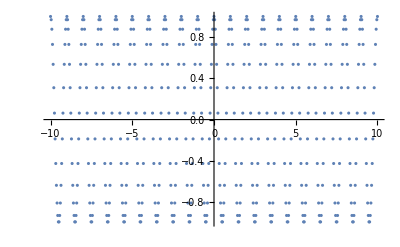

```mathematica
ListPlot[Transpose[{Sx, Sy}]]
```

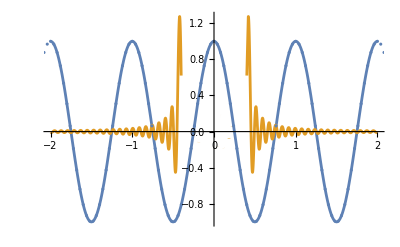

```mathematica
cft4[S_][t_]:=S.(sincn[(t-# T)/T ]&/@Sx)
Show[Plot[{f[x], cft4[Sy][x]}, {x, r1, r2}], ListPlot[Transpose[{Sx, Sy}]]]
```

```mathematica
InverseFourierTransform[Cosh[x] ,x]
```

InverseFourier::fftl: Argument Cosh[x] is not a non-empty list or rectangular array of numeric quantities.

InverseFourier[Cosh[x]]

```mathematica
InverseFourierTransform[Cosh[b], a, b]
```

InverseFourierTransform[Cosh[b],a,b]

```mathematica
TraditionalForm[a+E^(i x)]
```

a+ⅇ^(i x)

```mathematica
root[n_][x_]:=2Sin[x]+(Table[(-1)^i, {i, n}].Drop[NestList[Sin, x, n], 1])
```

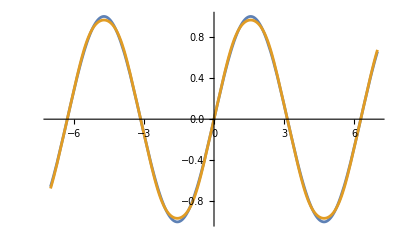

```mathematica
Plot[{Sin[x],root[3][root[3][x]]}, {x, -7,7}]
```

```mathematica
Plot[{Sin[x],root[1007][root[1007][x]]/1.5}, {x, -7,7}]
```

$Aborted

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10]}

a[1] Sin[x]+a[2] Sin[Sin[x]]+a[3] Sin[Sin[Sin[x]]]+a[4] Sin[Sin[Sin[Sin[x]]]]+a[5] Sin[Sin[Sin[Sin[Sin[x]]]]]+a[6] Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]+a[7] Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]+a[8] Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]]+a[9] Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]]]+a[10] Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]]]]

NIntegrate::inumr: The integrand (-Sin[x]+a[1] Sin[a[1] Sin[x]+a[2] Sin[Sin[«1»]]+a[3] Sin[Sin[«1»]]+a[4] Sin[Sin[«1»]]+a[5] Sin[Sin[«1»]]+a[6] Sin[Sin[«1»]]+a[7] Sin[Sin[«1»]]+a[8] Sin[Sin[«1»]]+a[9] Sin[Sin[«1»]]+a[10] Sin[Sin[«1»]]]+«8»+a[10] Sin[Sin[Sin[Sin[Sin[«1»]]]]])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-Sin[x]+a[1] Sin[a[1] Sin[x]+a[2] Sin[Sin[«1»]]+a[3] Sin[Sin[«1»]]+a[4] Sin[Sin[«1»]]+a[5] Sin[Sin[«1»]]+a[6] Sin[Sin[«1»]]+a[7] Sin[Sin[«1»]]+a[8] Sin[Sin[«1»]]+a[9] Sin[Sin[«1»]]+a[10] Sin[Sin[«1»]]]+«8»+a[10] Sin[Sin[Sin[Sin[Sin[«1»]]]]])^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6.28319,0.}}.

{1.52392×10^-6,{a[1]→-3.61897,a[2]→6.22319,a[3]→-1.9878,a[4]→-2.85394,a[5]→-1.28695,a[6]→-0.222112,a[7]→2.18777,a[8]→2.64449,a[9]→0.0929135,a[10]→-2.17973}}

-3.61897 Sin[y]+6.22319 Sin[Sin[y]]-1.9878 Sin[Sin[Sin[y]]]-2.85394 Sin[Sin[Sin[Sin[y]]]]-1.28695 Sin[Sin[Sin[Sin[Sin[y]]]]]-0.222112 Sin[Sin[Sin[Sin[Sin[Sin[y]]]]]]+2.18777 Sin[Sin[Sin[Sin[Sin[Sin[Sin[y]]]]]]]+2.64449 Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[y]]]]]]]]+0.0929135 Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[y]]]]]]]]]-2.17973 Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[y]]]]]]]]]]

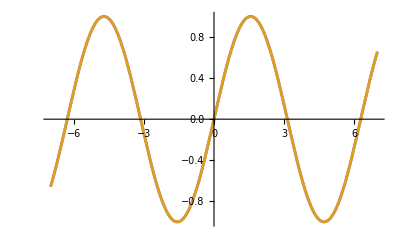

```mathematica
Manipulate[Plot[{Sin[x],root[n][root[n][x]]}, {x, -7,7}],{n,1,11,1}]
```

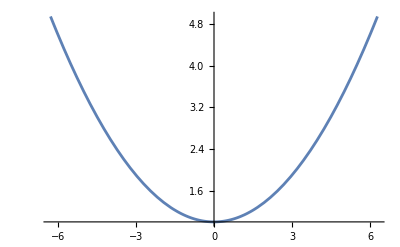

```mathematica
f[x_]:=1+x^2/10
range={-2Pi, 2Pi};
Plot[f[x], {x, range[[1]], range[[2]]}]
```

```mathematica
n=3;
params=Expand@N@(Table[a[i], {i, n}].Drop[NestList[f, x, n],1])
coefs=SymmetricDifference[{x},FixedPoint[Flatten[(If[#[[0]]===a,#,List@@#])&/@#]&,params]]
```

1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+0.02 x^2 a[2.]+0.001 x^4 a[2.]+1.121 a[3.]+0.0044 x^2 a[3.]+0.00026 x^4 a[3.]+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.]

Thread::tdlen: Objects of unequal length in {1.,a[1.]}+{0.1,x^2,a[1.]}+{1.1,a[2.]}+{0.02,x^2,a[2.]}+{0.001,x^4,a[2.]}+{1.121,a[3.]}+{0.0044,x^2,a[3.]}+{0.00026,x^4,a[3.]}+{4.×10^-6,x^6,a[3.]}+{1.×10^-7,x^8,a[3.]} cannot be combined.

Thread::tdlen: Objects of unequal length in {1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]} cannot be combined.

SymmetricDifference::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

SymmetricDifference[{x},{1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]}]

```mathematica
errorInt[func_]:=NIntegrate[(func[func[x]]-f[x])^2, {x, range[[1]], range[[2]]}]



solo=NMinimize[errorInt[params/.x->#&], coefs, Method->"NelderMead"]

eq=params/.Last[solo]/.x->y
af[x_]:=eq/.y->x

Plot[{f[x], af[af[x]]}, {x, range[[1]], range[[2]]}]
```

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

SymmetricDifference::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::nlim: x = Compile`$7 is not a valid limit of integration.

NMinimize::nnum: The function value NIntegrate[((params/.x→#1&)[(params/.x→Slot[«1»]&)[x]]-f[x])^2,{x,{-2 π,2 π}⟦1⟧,{-2 π,2 π}⟦2⟧}] is not a number at {SymmetricDifference[{x},{1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]}]} = {-0.829053}.

NMinimize::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::nlim: x = Compile`$7 is not a valid limit of integration.

NMinimize::nnum: The function value NIntegrate[((params/.x→#1&)[(params/.x→Slot[«1»]&)[x]]-f[x])^2,{x,{-2 π,2 π}⟦1⟧,{-2 π,2 π}⟦2⟧}] is not a number at {SymmetricDifference[{x},{1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]}]} = {-0.829053}.

NMinimize[NIntegrate[((params/.x→#1&)[(params/.x→#1&)[x]]-f[x])^2,{x,range⟦1⟧,range⟦2⟧}],SymmetricDifference[{x},{1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]}],Method→NelderMead]

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

SymmetricDifference::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::heads: Heads List and Plus at positions 1 and 2 are expected to be the same.

NIntegrate::inumr: The integrand (-1-x^2/10+«8»+4.×10^-6 a[3.] (1. a[1.]+«1»+«6»+«1»+«23» x^8 a[3.])^6+1.×10^-7 a[3.] (1. a[1.]+0.1 x^2 a[1.]+1.1 a[2.]+«5»+4.×10^-6 x^6 a[3.]+1.×10^-7 x^8 a[3.])^8)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::nlim: x = Compile`$7 is not a valid limit of integration.

NMinimize::nnum: The function value NIntegrate[((params/.x→#1&)[(params/.x→Slot[«1»]&)[x]]-f[x])^2,{x,{-2 π,2 π}⟦1⟧,{-2 π,2 π}⟦2⟧}] is not a number at {SymmetricDifference[{x},{1.,a[1.]}+{1.1,a[2.]}+{1.121,a[3.]}+{1.×10^-7,x^8,a[3.]}+{4.×10^-6,x^6,a[3.]}+{0.00026,x^4,a[3.]}+{0.001,x^4,a[2.]}+{0.0044,x^2,a[3.]}+{0.02,x^2,a[2.]}+{0.1,x^2,a[1.]}]} = {-0.829053}.

1. a[1.]+0.1 y^2 a[1.]+1.1 a[2.]+0.02 y^2 a[2.]+0.001 y^4 a[2.]+1.121 a[3.]+0.0044 y^2 a[3.]+0.00026 y^4 a[3.]+4.×10^-6 y^6 a[3.]+1.×10^-7 y^8 a[3.]

-Graphics-

```mathematica
params=(a[1]+a[2]Sin[a[3]x])
```

a[1]+a[2] Sin[x a[3]]

{a[1],a[2],a[1],x,a[3]}